```mathematica
data=RandomVariate[MultinormalDistribution[{0,0,0},{{1,0.5,0.3},{0.5,1,0.5},{0.3,0.5,1}}],1000];
ListPointPlot3D[data,PlotStyle->PointSize[0.02]]
```

```mathematica
Manipulate[Module[{data,rotatedData,scaledData,plot},(*生成一个三维高斯分布的随机样本*)data=RandomVariate[NormalDistribution[],{100,3}];
(*构造绕 z 轴旋转的旋转矩阵*)rotationMatrix=RotationMatrix[θ,{0,0,1}];
(*构造缩放矩阵*)scalingMatrix=DiagonalMatrix[{s,s,1}];
(*应用旋转和缩放变换*)rotatedData=data.rotationMatrix;
scaledData=rotatedData.scalingMatrix;
(*绘制散点图*)plot=ListPointPlot3D[scaledData,PlotRange->{{-3,3},{-3,3},{-3,3}},PlotStyle->PointSize[0.02],BoxRatios->{1,1,1},Axes->True];
(*返回绘制的图形*)plot],{{θ,0,"Rotation Angle"},0,2 π,Appearance->"Labeled"},{{s,1,"Scaling Factor"},0.1,2,Appearance->"Labeled"}]
```

```mathematica
(*生成随机的协方差矩阵*)cov=RandomReal[{-1,1},{3,3}];
cov=cov.Transpose[cov];(*确保协方差矩阵是对称正定的*)(*生成高斯分布的随机样本*)data=RandomVariate[MultinormalDistribution[{0,0,0},cov],1000];

(*计算每个点的概率密度值*)
pdfValues=PDF[MultinormalDistribution[{0,0,0},cov],#]&/@data;

(*将概率密度值映射到颜色值*)
colors=ColorData["TemperatureMap"]/@Rescale[pdfValues];

(*绘制带颜色的点*)
Graphics3D[MapThread[{#1,Point[#2]}&,{colors,data}],Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,ImageSize->400]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ClearAll["Global`*"]
Manipulate[
Module[{rotationMatrix,scalingMatrix,graphics, data, pdfValues, colors, graphics1, graphics2, graphics3, graphics4},
(*放缩矩阵*)
scalingMatrix=ScalingMatrix[{sx,sy,sz}];

(*旋转矩阵*)
rotationMatrix=RotationMatrix[θ,{1,0,0}].RotationMatrix[φ,{0,1,0}];

(*协方差矩阵*)
cov = rotationMatrix.scalingMatrix.Transpose[scalingMatrix].Transpose[rotationMatrix];
cov2D=Take[cov, 2, 2];
myGaussian1D := {qx, qy, z}.Inverse[cov].{qx, qy, z};

(*高斯分布的随机样本*)
data=RandomVariate[MultinormalDistribution[{0,0,0},cov],10];

(*计算每个样本点的概率密度值*)
pdfValues=PDF[MultinormalDistribution[{0,0,0},cov],data];

(*根据概率密度值映射颜色*)
colors=ColorData["Rainbow"]/@Rescale[pdfValues];


(*创建长方体的图形*)
graphics1=Graphics3D[
{EdgeForm[None],FaceForm[LightBlue],
GeometricTransformation[Cuboid[{-1/2, -1/2,-1/2}],
rotationMatrix.scalingMatrix]},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->400,
ViewPoint->{0,0,Infinity}
];

(*创建球体的图形*)
graphics2=Graphics3D[
{Opacity[0.5],Blue,GeometricTransformation[Sphere[],rotationMatrix.scalingMatrix],
Red,Thickness[0.02],Line[{{qx,qy,-2},{qx,qy,2}}]
},
Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},
PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->400,
ViewPoint->{0,0,Infinity}
];

(*绘制点*)
graphics3=Graphics3D[
{PointSize[0.01],
MapThread[{#1,Point[#2]}&,{colors,data}]
},
Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},
PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->400,
ViewPoint->{0,0,Infinity}
];

(*splatting*)
graphics4 = ContourPlot[
PDF[MultinormalDistribution[{0,0},cov2D],{x,y}],
{x,-2,2},{y,-2,2},Contours->{0.05,0.1,0.2},
ContourStyle->Directive[Opacity[0.5],ColorData["BlueGreenYellow"]],FrameLabel->{"x","y"},AspectRatio->Automatic,
ImageSize->400,
Epilog->{Red,PointSize[0.02],Point[{qx,qy}]}
];

(*1DGS*)
sigma = Sqrt[1/Inverse[cov][[3]][[3]]];
mxval = FindMaxValue[Exp[-myGaussian1D], z];
mxx = FindArgMax[Exp[-myGaussian1D], z][[1]];
graphics5 = Plot[
{Exp[-(myGaussian1D)], Piecewise[{{mxval,z≥-sigma+mxx&&z≤sigma+mxx},{Indeterminate,True}}]},
{z,-2,2},
PlotRange->{Automatic, {0, 1.1}},AxesLabel->{"z",Text[Exp[-1/2(myGaussian1D)]//Simplify]},
ImageSize->  400
];

(*返回图形*)
Column[{
Row[{Text["cov3D: "], MatrixForm[cov], Text["  cov2D: "], MatrixForm[cov2D]}],
Row[{graphics2, graphics4}],
Row[{Text[Simplify[myGaussian1D, z]]}],
Row[{graphics5, "sigma:", sigma,"; mu:", mxx, "; mxval:", mxval}]
}]
],

{{θ,0,"X Rotation Angle"},-π,π,Appearance->"Labeled"},
{{φ,0,"Y Rotation Angle"},-π,π,Appearance->"Labeled"},
{{sx,1,"X Scaling Factor"},0.1,2,Appearance->"Labeled"},
{{sy,1,"Y Scaling Factor"},0.1,2,Appearance->"Labeled"},
{{sz,1,"Z Scaling Factor"},0.1,2,Appearance->"Labeled"},
{{qx,0,"query x"},-2,2,Appearance->"Labeled"},
{{qy,0,"query y"},-2,2,Appearance->"Labeled"}
]
```

MultinormalDistribution::posdefprm: The value {{1.08157,0.000103878,0.00102981},{0.000103878,1.0404,2.5981×10^-6},{0.00102981,2.5981×10^-6,1.04043}} at position 2 in MultinormalDistribution[{0,0,0},{{1.08157,0.000103878,0.00102981},{0.000103878,1.0404,2.5981×10^-6},{0.00102981,2.5981×10^-6,1.04043}}] is expected to be a symmetric positive definite matrix.

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

MapThread::mptd: Object Rescale[Blend[Rainbow,PDF[MultinormalDistribution[{0,0,0},{{1.08157,0.000103878,0.00102981},{0.000103878,1.0404,2.5981×10^-6},{0.00102981,2.5981×10^-6,1.04043}}],RandomVariate[«1»]]]] at position {2, 1} in MapThread[{#1,Point[#2]}&,{Rescale[Blend[Rainbow,PDF[MultinormalDistribution[{0,0,0},{{«3»},{«3»},{«3»}}],RandomVariate[MultinormalDistribution[{«3»},{«3»}],10]]]],RandomVariate[MultinormalDistribution[{0,0,0},{{1.08157,«22»,0.00102981},{«1»},«1»}],10]}] has only 0 of required 1 dimensions.

MultinormalDistribution::posdefprm: The value {{1.08157,0.000103878,0.00102981},{0.000103878,1.0404,2.5981×10^-6},{0.00102981,2.5981×10^-6,1.04043}} at position 2 in MultinormalDistribution[{0,0,0},{{1.08157,0.000103878,0.00102981},{0.000103878,1.0404,2.5981×10^-6},{0.00102981,2.5981×10^-6,1.04043}}] is expected to be a symmetric positive definite matrix.

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

MapThread::mptd: Object Rescale[Blend[Rainbow,PDF[MultinormalDistribution[{0,0,0},{{1.08157,0.000103878,0.00102981},{0.000103878,1.0404,2.5981×10^-6},{0.00102981,2.5981×10^-6,1.04043}}],RandomVariate[«1»]]]] at position {2, 1} in MapThread[{#1,Point[#2]}&,{Rescale[Blend[Rainbow,PDF[MultinormalDistribution[{0,0,0},{{«3»},{«3»},{«3»}}],RandomVariate[MultinormalDistribution[{«3»},{«3»}],10]]]],RandomVariate[MultinormalDistribution[{0,0,0},{{1.08157,«22»,0.00102981},{«1»},«1»}],10]}] has only 0 of required 1 dimensions.

```mathematica
res = {x, y, z}.{{a0, a1, a2}, {a1, a3, a4}, {a2, a4, a5}}.{{x}, {y}, {z}};
res
coef = CoefficientList[res, z][[1]]
a = coef[[3]]
b = coef[[2]]
c = coef[[1]]
```

{x (a0 x+a1 y+a2 z)+y (a1 x+a3 y+a4 z)+z (a2 x+a4 y+a5 z)}

{a0 x^2+2 a1 x y+a3 y^2,2 a2 x+2 a4 y,a5}

a5

2 a2 x+2 a4 y

a0 x^2+2 a1 x y+a3 y^2

```mathematica
res = {x, y, z}.{{a,b, c}, {b, d, e}, {c, e,f}}.{{x}, {y}, {z}}
res//Expand[#, z]&
coef = CoefficientList[res, z][[1]]
```

{x (a x+b y+c z)+y (b x+d y+e z)+z (c x+e y+f z)}

{a x^2+2 b x y+d y^2+2 c x z+2 e y z+f z^2}

{a x^2+2 b x y+d y^2,2 c x+2 e y,f}

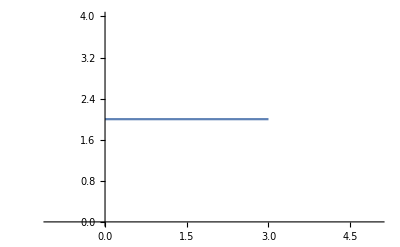

```mathematica
Plot[Piecewise[{{2,x≥0&&x≤3},{Indeterminate,True}}],{x,-1,5}]
```